```mathematica
Monitor[Table[allGraphs6[k,"generators"]=FlatGenerators[allGraphs6[k,"colofour"]],{k,Sort[Keys[allGraphs6]]}],k];
```

```mathematica
FullBaseCoeff6[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs6[#,"colofour"]&,allGraphs6AtomKeys]}],CompareSymbols]}]
```

```mathematica
Sort[Table[var,{var,Map[allGraphs6[#,"colofour"]&,allGraphs6AtomKeys]}],CompareSymbols]
```

```mathematica
EmptyBaseCoeff6[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Map[allGraphs6[#,"colofourrealnull"]&,allGraphs6NullAtomKeys]}],CompareSymbols]}]
```

```mathematica
FullBaseCoeff6[allGraphs6[0,"colofour"]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
theGens=Sort[Select[Keys[allGraphs6],VertexCount[allGraphs6[#,"graph"]]==6&&Length[ListofVars[allGraphs6[#,"generators"]]]==1&],CompareSymbols[First[allGraphs6[#1,"generators"]],First[allGraphs6[#2,"generators"]]]&];
```

```mathematica
ShowGraph[allGraphs6,273]
```

-Graphics-273

```mathematica
ShowGraph[allGraphs6,1771551]
```

-Graphics-1771551

```mathematica
4783213
```

```mathematica
BaseGenerators[allGraphs6[61479,"colofour"]]
```

<|2→{v145x236,v135x246,v124x356,v123x456},3→{v15x24x36,v15x23x46,v14x26x35,v14x23x56,v13x26x45,v13x24x56,v12x36x45,v12x35x46}|>

```mathematica
DocValue[key_]:=With[
{rep=Join[
Table[ChangeSymbol[k,"g"]->Style[ChangeSymbol[k,"g"],Red,Bold],{k,FlatGenerators[allGraphs6[key,"generators"]]}],
Table[k->Style[k,Red],{k,FlatGenerators[allGraphs6[key,"generators"]]}]]},
Table[allGraphs6[key,code]/.rep,{code,{"generators","genfour","colofour"}}]
]
```

```mathematica
GenIndices[key_]:=Block[{gens=Map[ChangeSymbol[#,"g"]&,FlatGenerators[allGraphs6[key,"generators"]]],gens2=Map[ChangeSymbol[#,"v"]&,FlatGenerators[allGraphs6[key,"generators"]]],genForm=allGraphs6[key,"genfour"],
genColor=allGraphs6[key,"colofour"]},
With[{a=Table[Coefficient[genForm,var],{var,gens}],b=Table[Coefficient[genColor,var],{var,gens2}]},
{
a,
b,
a==b
}
]
]
```

```mathematica
Table[ShowGraph[allGraphs6,k]->GenIndices[k],{k,Take[Keys[allGraphs6],20]}]
```

{-Graphics-0→{{1},{1},True},-Graphics-4782969→{{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},True},-Graphics-6377292→{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},True},-Graphics-6908733→{{1,1,1,1},{1,1,1,1},True},-Graphics-7085880→{{1,1},{1,1},True},-Graphics-7144929→{{1},{1},True},-Graphics-7164612→{{1,1,1,1,1,1,1,1},{1,1,1,1,1,1,1,1},True},-Graphics-7171173→{{1,1,1,1},{1,1,1,1},True},-Graphics-7173360→{{1,1},{1,1},True},-Graphics-7174089→{{1},{1},True},-Graphics-7174332→{{1,1,1,1},{1,1,1,1},True},-Graphics-7174413→{{1,1},{1,1},True},-Graphics-7174440→{{1},{1},True},-Graphics-7174449→{{1,1},{1,1},True},-Graphics-7174452→{{1},{1},True},-Graphics-7174453→{{1},{1},True},-Graphics-7174454→{{1},{1},True},-Graphics-7174456→{{1},{1},True},-Graphics-7174450→{{1},{1},True},-Graphics-7174458→{{1},{1},True}}

```mathematica
Table[ShowGraph[allGraphs6,k]->DocValue[k],{k,Take[Keys[allGraphs6],10]}]
```

{-Graphics-0→{{v123456},g123456,v12345x6+v12346x5+v1234x56+v1234x5x6+v12356x4+v1235x46+v1235x4x6+v1236x45+v1236x4x5+v123x456+v123x45x6+v123x46x5+v123x4x56+v123x4x5x6+v12456x3+v1245x36+v1245x3x6+v1246x35+v1246x3x5+v124x356+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6+v1256x34+v1256x3x4+v125x346+v125x34x6+v125x36x4+v125x3x46+v125x3x4x6+v126x345+v126x34x5+v126x35x4+v126x3x45+v126x3x4x5+v12x3456+v12x345x6+v12x346x5+v12x34x56+v12x34x5x6+v12x356x4+v12x35x46+v12x35x4x6+v12x36x45+v12x36x4x5+v12x3x456+v12x3x45x6+v12x3x46x5+v12x3x4x56+v12x3x4x5x6+v13456x2+v1345x26+v1345x2x6+v1346x25+v1346x2x5+v134x256+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6+v1356x24+v1356x2x4+v135x246+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v136x245+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v13x2456+v13x245x6+v13x246x5+v13x24x56+v13x24x5x6+v13x256x4+v13x25x46+v13x25x4x6+v13x26x45+v13x26x4x5+v13x2x456+v13x2x45x6+v13x2x46x5+v13x2x4x56+v13x2x4x5x6+v1456x23+v1456x2x3+v145x236+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x235+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x2356+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6+v14x256x3+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x356+v14x2x35x6+v14x2x36x5+v14x2x3x56+v14x2x3x5x6+v156x234+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v15x2346+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x2345+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x23456+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v123456},-Graphics-4782969→{{v1x23456,v16x2345,v15x2346,v156x234,v14x2356,v146x235,v145x236,v1456x23,v13x2456,v136x245,v135x246,v1356x24,v134x256,v1346x25,v1345x26,v13456x2},-g1345x2x6-g1346x2x5-g134x25x6-g134x26x5-g134x2x56+2 g134x2x5x6-g1356x2x4-g135x24x6-g135x26x4-g135x2x46+2 g135x2x4x6-g136x24x5-g136x25x4-g136x2x45+2 g136x2x4x5-g13x245x6-g13x246x5-g13x24x56+2 g13x24x5x6-g13x256x4-g13x25x46+2 g13x25x4x6-g13x26x45+2 g13x26x4x5-g13x2x456+2 g13x2x45x6+2 g13x2x46x5+2 g13x2x4x56-6 g13x2x4x5x6-g1456x2x3-g145x23x6-g145x26x3-g145x2x36+2 g145x2x3x6-g146x23x5-g146x25x3-g146x2x35+2 g146x2x3x5-g14x235x6-g14x236x5-g14x23x56+2 g14x23x5x6-g14x256x3-g14x25x36+2 g14x25x3x6-g14x26x35+2 g14x26x3x5-g14x2x356+2 g14x2x35x6+2 g14x2x36x5+2 g14x2x3x56-6 g14x2x3x5x6-g156x23x4-g156x24x3-g156x2x34+2 g156x2x3x4-g15x234x6-g15x236x4-g15x23x46+2 g15x23x4x6-g15x246x3-g15x24x36+2 g15x24x3x6-g15x26x34+2 g15x26x3x4-g15x2x346+2 g15x2x34x6+2 g15x2x36x4+2 g15x2x3x46-6 g15x2x3x4x6-g16x234x5-g16x235x4-g16x23x45+2 g16x23x4x5-g16x245x3-g16x24x35+2 g16x24x3x5-g16x25x34+2 g16x25x3x4-g16x2x345+2 g16x2x34x5+2 g16x2x35x4+2 g16x2x3x45-6 g16x2x3x4x5-g1x2345x6-g1x2346x5-g1x234x56+2 g1x234x5x6-g1x2356x4-g1x235x46+2 g1x235x4x6-g1x236x45+2 g1x236x4x5-g1x23x456+2 g1x23x45x6+2 g1x23x46x5+2 g1x23x4x56-6 g1x23x4x5x6-g1x2456x3-g1x245x36+2 g1x245x3x6-g1x246x35+2 g1x246x3x5-g1x24x356+2 g1x24x35x6+2 g1x24x36x5+2 g1x24x3x56-6 g1x24x3x5x6-g1x256x34+2 g1x256x3x4-g1x25x346+2 g1x25x34x6+2 g1x25x36x4+2 g1x25x3x46-6 g1x25x3x4x6-g1x26x345+2 g1x26x34x5+2 g1x26x35x4+2 g1x26x3x45-6 g1x26x3x4x5-g1x2x3456+2 g1x2x345x6+2 g1x2x346x5+2 g1x2x34x56-6 g1x2x34x5x6+2 g1x2x356x4+2 g1x2x35x46-6 g1x2x35x4x6+2 g1x2x36x45-6 g1x2x36x4x5+2 g1x2x3x456-6 g1x2x3x45x6-6 g1x2x3x46x5-6 g1x2x3x4x56+24 g1x2x3x4x5x6+g13456x2+g1345x26+g1346x25+g134x256+g1356x24+g135x246+g136x245+g13x2456+g1456x23+g145x236+g146x235+g14x2356+g156x234+g15x2346+g16x2345+g1x23456,v1345x2x6+v1346x2x5+v134x25x6+v134x26x5+v134x2x56+v134x2x5x6+v1356x2x4+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v136x24x5+v136x25x4+v136x2x45+v136x2x4x5+v13x245x6+v13x246x5+v13x24x56+v13x24x5x6+v13x256x4+v13x25x46+v13x25x4x6+v13x26x45+v13x26x4x5+v13x2x456+v13x2x45x6+v13x2x46x5+v13x2x4x56+v13x2x4x5x6+v1456x2x3+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6+v14x256x3+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x356+v14x2x35x6+v14x2x36x5+v14x2x3x56+v14x2x3x5x6+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v13456x2+v1345x26+v1346x25+v134x256+v1356x24+v135x246+v136x245+v13x2456+v1456x23+v145x236+v146x235+v14x2356+v156x234+v15x2346+v16x2345+v1x23456},-Graphics-6377292→{{v1x23456,v16x2345,v15x2346,v156x234,v14x2356,v146x235,v145x236,v1456x23},-g145x23x6-g146x23x5-g14x235x6-g14x236x5-g14x23x56+2 g14x23x5x6-g156x23x4-g15x234x6-g15x236x4-g15x23x46+2 g15x23x4x6-g16x234x5-g16x235x4-g16x23x45+2 g16x23x4x5-g1x2345x6-g1x2346x5-g1x234x56+2 g1x234x5x6-g1x2356x4-g1x235x46+2 g1x235x4x6-g1x236x45+2 g1x236x4x5-g1x23x456+2 g1x23x45x6+2 g1x23x46x5+2 g1x23x4x56-6 g1x23x4x5x6+g1456x23+g145x236+g146x235+g14x2356+g156x234+g15x2346+g16x2345+g1x23456,v1456x2x3+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v146x23x5+v146x25x3+v146x2x35+v146x2x3x5+v14x235x6+v14x236x5+v14x23x56+v14x23x5x6+v14x256x3+v14x25x36+v14x25x3x6+v14x26x35+v14x26x3x5+v14x2x356+v14x2x35x6+v14x2x36x5+v14x2x3x56+v14x2x3x5x6+v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v1456x23+v145x236+v146x235+v14x2356+v156x234+v15x2346+v16x2345+v1x23456},-Graphics-6908733→{{v1x23456,v16x2345,v15x2346,v156x234},-g15x234x6-g16x234x5-g1x2345x6-g1x2346x5-g1x234x56+2 g1x234x5x6+g156x234+g15x2346+g16x2345+g1x23456,v156x23x4+v156x24x3+v156x2x34+v156x2x3x4+v15x234x6+v15x236x4+v15x23x46+v15x23x4x6+v15x246x3+v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x346+v15x2x34x6+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v156x234+v15x2346+v16x2345+v1x23456},-Graphics-7085880→{{v1x23456,v16x2345},-g1x2345x6+g16x2345+g1x23456,v16x234x5+v16x235x4+v16x23x45+v16x23x4x5+v16x245x3+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x345+v16x2x34x5+v16x2x35x4+v16x2x3x45+v16x2x3x4x5+v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v16x2345+v1x23456},-Graphics-7144929→{{v1x23456},g1x23456,v1x2345x6+v1x2346x5+v1x234x56+v1x234x5x6+v1x2356x4+v1x235x46+v1x235x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x2456x3+v1x245x36+v1x245x3x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x34+v1x256x3x4+v1x25x346+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x345+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x3456+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v1x23456},-Graphics-7164612→{{v1x2x3456,v1x26x345,v1x25x346,v1x256x34,v1x24x356,v1x246x35,v1x245x36,v1x2456x3},-g1x245x3x6-g1x246x3x5-g1x24x35x6-g1x24x36x5-g1x24x3x56+2 g1x24x3x5x6-g1x256x3x4-g1x25x34x6-g1x25x36x4-g1x25x3x46+2 g1x25x3x4x6-g1x26x34x5-g1x26x35x4-g1x26x3x45+2 g1x26x3x4x5-g1x2x345x6-g1x2x346x5-g1x2x34x56+2 g1x2x34x5x6-g1x2x356x4-g1x2x35x46+2 g1x2x35x4x6-g1x2x36x45+2 g1x2x36x4x5-g1x2x3x456+2 g1x2x3x45x6+2 g1x2x3x46x5+2 g1x2x3x4x56-6 g1x2x3x4x5x6+g1x2456x3+g1x245x36+g1x246x35+g1x24x356+g1x256x34+g1x25x346+g1x26x345+g1x2x3456,v1x245x3x6+v1x246x3x5+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x256x3x4+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v1x2456x3+v1x245x36+v1x246x35+v1x24x356+v1x256x34+v1x25x346+v1x26x345+v1x2x3456},-Graphics-7171173→{{v1x2x3456,v1x26x345,v1x25x346,v1x256x34},-g1x25x34x6-g1x26x34x5-g1x2x345x6-g1x2x346x5-g1x2x34x56+2 g1x2x34x5x6+g1x256x34+g1x25x346+g1x26x345+g1x2x3456,v1x256x3x4+v1x25x34x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v1x256x34+v1x25x346+v1x26x345+v1x2x3456},-Graphics-7173360→{{v1x2x3456,v1x26x345},-g1x2x345x6+g1x26x345+g1x2x3456,v1x26x34x5+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v1x26x345+v1x2x3456},-Graphics-7174089→{{v1x2x3456},g1x2x3456,v1x2x345x6+v1x2x346x5+v1x2x34x56+v1x2x34x5x6+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v1x2x3456}}

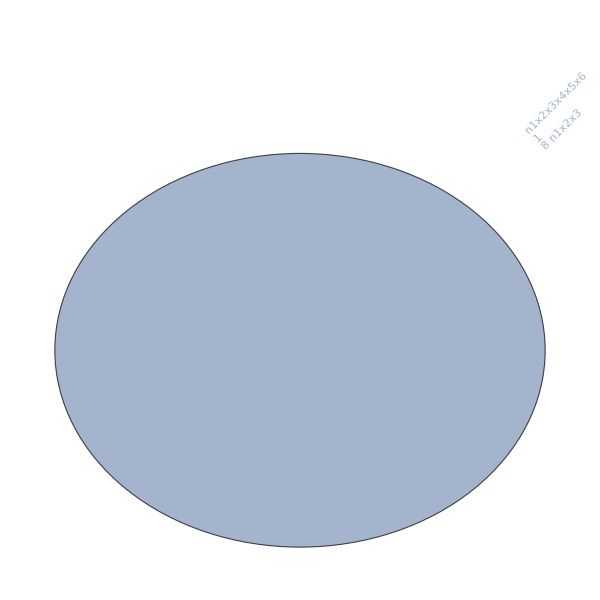

```mathematica
MobiusGraph4[0,allGraphs6]
```

```mathematica
With[
{rep=Join[
Table[ChangeSymbol[k,"g"]->Style[ChangeSymbol[k,"g"],Red,Bold],{k,FlatGenerators[allGraphs6[61479,"generators"]]}],
Table[k->Style[k,Red],{k,FlatGenerators[allGraphs6[61479,"generators"]]}]]},
Table[allGraphs6[61479,code]/.rep,{code,{"generators","genfour","colofour"}}]
]
```

{{v145x236,v135x246,v124x356,v123x456,v15x24x36,v15x23x46,v14x26x35,v14x23x56,v13x26x45,v13x24x56,v12x36x45,v12x35x46},-g12x35x4x6-g12x36x4x5-g12x3x45x6-g12x3x46x5-g12x3x4x56+2 g12x3x4x5x6-g13x24x5x6-g13x26x4x5-g13x2x45x6-g13x2x46x5-g13x2x4x56+2 g13x2x4x5x6-g14x23x5x6-g14x26x3x5-g14x2x35x6-g14x2x36x5-g14x2x3x56+2 g14x2x3x5x6-g15x23x4x6-g15x24x3x6-g15x26x3x4-g15x2x36x4-g15x2x3x46+2 g15x2x3x4x6-g1x23x45x6-g1x23x46x5-g1x23x4x56+2 g1x23x4x5x6-g1x24x35x6-g1x24x36x5-g1x24x3x56+2 g1x24x3x5x6-g1x26x35x4-g1x26x3x45+2 g1x26x3x4x5-g1x2x35x46+2 g1x2x35x4x6-g1x2x36x45+2 g1x2x36x4x5+2 g1x2x3x45x6+2 g1x2x3x46x5+2 g1x2x3x4x56-5 g1x2x3x4x5x6+g123x456+g124x356+g12x35x46+g12x36x45+g135x246+g13x24x56+g13x26x45+g145x236+g14x23x56+g14x26x35+g15x23x46+g15x24x36,v123x45x6+v123x46x5+v123x4x56+v123x4x5x6+v124x35x6+v124x36x5+v124x3x56+v124x3x5x6+v12x356x4+v12x35x4x6+v12x36x4x5+v12x3x456+v12x3x45x6+v12x3x46x5+v12x3x4x56+v12x3x4x5x6+v135x24x6+v135x26x4+v135x2x46+v135x2x4x6+v13x246x5+v13x24x5x6+v13x26x4x5+v13x2x456+v13x2x45x6+v13x2x46x5+v13x2x4x56+v13x2x4x5x6+v145x23x6+v145x26x3+v145x2x36+v145x2x3x6+v14x236x5+v14x23x5x6+v14x26x3x5+v14x2x356+v14x2x35x6+v14x2x36x5+v14x2x3x56+v14x2x3x5x6+v15x236x4+v15x23x4x6+v15x246x3+v15x24x3x6+v15x26x3x4+v15x2x36x4+v15x2x3x46+v15x2x3x4x6+v1x236x45+v1x236x4x5+v1x23x456+v1x23x45x6+v1x23x46x5+v1x23x4x56+v1x23x4x5x6+v1x246x35+v1x246x3x5+v1x24x356+v1x24x35x6+v1x24x36x5+v1x24x3x56+v1x24x3x5x6+v1x26x35x4+v1x26x3x45+v1x26x3x4x5+v1x2x356x4+v1x2x35x46+v1x2x35x4x6+v1x2x36x45+v1x2x36x4x5+v1x2x3x456+v1x2x3x45x6+v1x2x3x46x5+v1x2x3x4x56+v1x2x3x4x5x6+v123x456+v124x356+v12x35x46+v12x36x45+v135x246+v13x24x56+v13x26x45+v145x236+v14x23x56+v14x26x35+v15x23x46+v15x24x36}

```mathematica
ChangeSymbol[s_,prefix_]:=Symbol[StringReplace[SymbolName[s],"v"->prefix]]
```

```mathematica
repGen=First[Solve[Table[ChangeSymbol[First[allGraphs6[k,"generators"]],"g"]==allGraphs6[k,"colofour"],{k,theGens}],Table[allGraphs6[m,"colofour"],{m,allGraphs6AtomKeys}]]];
```

```mathematica
Monitor[Table[allGraphs6[k,"genfour"]=Simplify[allGraphs6[k,"colofour"]/.repGen],{k,Sort[Keys[allGraphs6]]}],k];
```

```mathematica
GenBaseCoeff[form_]:=Table[Coefficient[form,var],{var,Sort[Table[var2,{var2,Table[ChangeSymbol[First[allGraphs6[k,"generators"]],"g"],{k,theGens}]}],CompareSymbols]}]
```

```mathematica
GenBaseCoeff[allGraphs6[61479,"genfour"]].Transpose[EmptyBaseCoeff6[allGraphs6[61479,"genfour"]]]
```

Transpose::nmtx: The first two levels of {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,«153»} cannot be transposed.

{-5,2,2,2,0,2,2,2,2,0,2,2,2,2,2,0,0,-1,-1,-1,-1,-1,-1,-1,-1,0,0,0,-1,0,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,-1,0,-1,-1,-1,-1,-1,0,-1,-1,0,-1,-1,-1,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,0,1,1,0,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}.Transpose[{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}]

```mathematica
Table[With[{c=EmptyBaseCoeff6[allGraphs6[k,"colofourrealnull"]]},{Min[c],Max[c]}],{k,theGens}]//Tally
```

{{{-120,24},1},{{-96,24},15},{{-78,18},45},{{-54,18},20},{{-64,14},15},{{-46,14},60},{{-16,8},15},{{-31,7},10},{{-15,7},15},{{-1,1},6},{{0,1},1}}

```mathematica
EmptyBaseCoeff6[allGraphs6[61479,"colofourrealnull"]]
```

{1,0,0,0,-1,0,0,0,0,-1,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
theGensComp=Table[FindComplement[k,allGraphs6],{k,theGens}]
```

{0,1,9,3,243,81,27,19683,6561,2187,729,4782969,1594323,531441,177147,59049,244,84,36,19684,19692,19686,6562,6642,6588,2190,2430,2214,738,972,810,4782970,4782978,4782972,4783212,4783050,4782996,1594324,1594332,1594326,1600884,1596510,1595052,531442,531522,531468,551124,533628,532170,177150,177390,177174,196830,183708,177876,59058,59292,59130,78732,65610,61236,13,333,273,109,26487,21951,20439,8757,7293,2917,6396975,5320971,4962303,4842747,2126007,1771551,1653399,708597,590493,236197,4783213,4783053,4783005,1600885,1596513,1595061,551125,533655,532251,196833,183735,178119,78741,65691,61479,19696,26488,21954,20448,6670,8784,7374,2460,3160,1062,4782982,4783302,4783242,4783078,6396976,6396984,6396978,5320972,5321052,5320998,4962306,4962546,4962330,4842756,4842990,4842828,1594336,1603080,1601616,1597240,2126008,2128194,2126736,1771554,1778112,1772280,1653408,1659960,1655586,531550,553392,551880,534358,708624,728280,709326,590574,610176,592680,177420,203634,197586,184440,236440,255880,242758,59382,85536,81000,67806,364,28764,27246,22708,9490,6935220,6576390,6456780,5500314,5380752,5022082,2303244,2185086,1830628,767650,6396988,5321080,4962576,4843080,2128924,1778844,1662156,729036,612444,262684,4783333,6935221,6576393,6456789,5500341,5380833,5022325,1603813,2303973,2187273,1837189,554149,787333,204393,87813,29524,7114644,6995028,6636196,5560096,2362324,7174453}

```mathematica
SummarizeGenerators[k_]:=Block[{gen=BaseGenerators[allGraphs6[k,"colofour"]],keys},
keys=Keys[gen];
Table[{kk,Length[gen[kk]]},{kk,Sort[keys]}]]
```

```mathematica
SummarizeGenerators[61479]
```

{{2,4},{3,8}}

```mathematica
Table[SummarizeGenerators[k],{k,theGensComp}]
```

{{{1,1}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{6,1}}}

```mathematica
j={{{1,1}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,16}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{2,8}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{3,27}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{2,4},{3,8}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{3,18}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{4,16}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{3,6}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{4,12}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{5,5}},{{6,1}}};
```

```mathematica
TableForm[Tally[j], TableDepth->2]
```

{{1,1}} | 1
{{2,16}} | 15
{{2,8}} | 45
{{3,27}} | 20
{{2,4},{3,8}} | 15
{{3,18}} | 60
{{4,16}} | 15
{{3,6}} | 10
{{4,12}} | 15
{{5,5}} | 6
{{6,1}} | 1

```mathematica
Map[SymbolToLabel2[#,6]&,FlatGenerators[allGraphs6[273,"colofour"]]]//Length
```

27

```mathematica
Multicolumn[Table[Framed[Labeled[{
ShowGraph[allGraphs6,k],
ShowGraph[allGraphs6,FindComplement[k,allGraphs6]]
},SymbolToLabel2[allGraphs6[k,"generators"]//First,6],Top]],{k,theGens}],8,Appearance->"Horizontal"]
```

{-Graphics-7174453,-Graphics-0}OverHat[1] | {-Graphics-7174452,-Graphics-1}56 | {-Graphics-7174444,-Graphics-9}45 | {-Graphics-7174450,-Graphics-3}46 | {-Graphics-7174210,-Graphics-243}34 | {-Graphics-7174372,-Graphics-81}35 | {-Graphics-7174426,-Graphics-27}36 | {-Graphics-7154770,-Graphics-19683}23
{-Graphics-7167892,-Graphics-6561}24 | {-Graphics-7172266,-Graphics-2187}25 | {-Graphics-7173724,-Graphics-729}26 | {-Graphics-2391484,-Graphics-4782969}12 | {-Graphics-5580130,-Graphics-1594323}13 | {-Graphics-6643012,-Graphics-531441}14 | {-Graphics-6997306,-Graphics-177147}15 | {-Graphics-7115404,-Graphics-59049}16
{-Graphics-7174209,-Graphics-244}34♁56 | {-Graphics-7174369,-Graphics-84}35♁46 | {-Graphics-7174417,-Graphics-36}36♁45 | {-Graphics-7154769,-Graphics-19684}23♁56 | {-Graphics-7154761,-Graphics-19692}23♁45 | {-Graphics-7154767,-Graphics-19686}23♁46 | {-Graphics-7167891,-Graphics-6562}24♁56 | {-Graphics-7167811,-Graphics-6642}24♁35
{-Graphics-7167865,-Graphics-6588}24♁36 | {-Graphics-7172263,-Graphics-2190}25♁46 | {-Graphics-7172023,-Graphics-2430}25♁34 | {-Graphics-7172239,-Graphics-2214}25♁36 | {-Graphics-7173715,-Graphics-738}26♁45 | {-Graphics-7173481,-Graphics-972}26♁34 | {-Graphics-7173643,-Graphics-810}26♁35 | {-Graphics-2391483,-Graphics-4782970}12♁56
{-Graphics-2391475,-Graphics-4782978}12♁45 | {-Graphics-2391481,-Graphics-4782972}12♁46 | {-Graphics-2391241,-Graphics-4783212}12♁34 | {-Graphics-2391403,-Graphics-4783050}12♁35 | {-Graphics-2391457,-Graphics-4782996}12♁36 | {-Graphics-5580129,-Graphics-1594324}13♁56 | {-Graphics-5580121,-Graphics-1594332}13♁45 | {-Graphics-5580127,-Graphics-1594326}13♁46
{-Graphics-5573569,-Graphics-1600884}13♁24 | {-Graphics-5577943,-Graphics-1596510}13♁25 | {-Graphics-5579401,-Graphics-1595052}13♁26 | {-Graphics-6643011,-Graphics-531442}14♁56 | {-Graphics-6642931,-Graphics-531522}14♁35 | {-Graphics-6642985,-Graphics-531468}14♁36 | {-Graphics-6623329,-Graphics-551124}14♁23 | {-Graphics-6640825,-Graphics-533628}14♁25
{-Graphics-6642283,-Graphics-532170}14♁26 | {-Graphics-6997303,-Graphics-177150}15♁46 | {-Graphics-6997063,-Graphics-177390}15♁34 | {-Graphics-6997279,-Graphics-177174}15♁36 | {-Graphics-6977623,-Graphics-196830}15♁23 | {-Graphics-6990745,-Graphics-183708}15♁24 | {-Graphics-6996577,-Graphics-177876}15♁26 | {-Graphics-7115395,-Graphics-59058}16♁45
{-Graphics-7115161,-Graphics-59292}16♁34 | {-Graphics-7115323,-Graphics-59130}16♁35 | {-Graphics-7095721,-Graphics-78732}16♁23 | {-Graphics-7108843,-Graphics-65610}16♁24 | {-Graphics-7113217,-Graphics-61236}16♁25 | {-Graphics-7174440,-Graphics-13}456 | {-Graphics-7174120,-Graphics-333}345 | {-Graphics-7174180,-Graphics-273}346
{-Graphics-7174344,-Graphics-109}356 | {-Graphics-7147966,-Graphics-26487}234 | {-Graphics-7152502,-Graphics-21951}235 | {-Graphics-7154014,-Graphics-20439}236 | {-Graphics-7165696,-Graphics-8757}245 | {-Graphics-7167160,-Graphics-7293}246 | {-Graphics-7171536,-Graphics-2917}256 | {-Graphics-777478,-Graphics-6396975}123
{-Graphics-1853482,-Graphics-5320971}124 | {-Graphics-2212150,-Graphics-4962303}125 | {-Graphics-2331706,-Graphics-4842747}126 | {-Graphics-5048446,-Graphics-2126007}134 | {-Graphics-5402902,-Graphics-1771551}135 | {-Graphics-5521054,-Graphics-1653399}136 | {-Graphics-6465856,-Graphics-708597}145 | {-Graphics-6583960,-Graphics-590493}146
{-Graphics-6938256,-Graphics-236197}156 | {-Graphics-2391240,-Graphics-4783213}12♁34♁56 | {-Graphics-2391400,-Graphics-4783053}12♁35♁46 | {-Graphics-2391448,-Graphics-4783005}12♁36♁45 | {-Graphics-5573568,-Graphics-1600885}13♁24♁56 | {-Graphics-5577940,-Graphics-1596513}13♁25♁46 | {-Graphics-5579392,-Graphics-1595061}13♁26♁45 | {-Graphics-6623328,-Graphics-551125}14♁23♁56
{-Graphics-6640798,-Graphics-533655}14♁25♁36 | {-Graphics-6642202,-Graphics-532251}14♁26♁35 | {-Graphics-6977620,-Graphics-196833}15♁23♁46 | {-Graphics-6990718,-Graphics-183735}15♁24♁36 | {-Graphics-6996334,-Graphics-178119}15♁26♁34 | {-Graphics-7095712,-Graphics-78741}16♁23♁45 | {-Graphics-7108762,-Graphics-65691}16♁24♁35 | {-Graphics-7112974,-Graphics-61479}16♁25♁34
{-Graphics-7154757,-Graphics-19696}23♁456 | {-Graphics-7147965,-Graphics-26488}234♁56 | {-Graphics-7152499,-Graphics-21954}235♁46 | {-Graphics-7154005,-Graphics-20448}236♁45 | {-Graphics-7167783,-Graphics-6670}24♁356 | {-Graphics-7165669,-Graphics-8784}245♁36 | {-Graphics-7167079,-Graphics-7374}246♁35 | {-Graphics-7171993,-Graphics-2460}25♁346
{-Graphics-7171293,-Graphics-3160}256♁34 | {-Graphics-7173391,-Graphics-1062}26♁345 | {-Graphics-2391471,-Graphics-4782982}12♁456 | {-Graphics-2391151,-Graphics-4783302}12♁345 | {-Graphics-2391211,-Graphics-4783242}12♁346 | {-Graphics-2391375,-Graphics-4783078}12♁356 | {-Graphics-777477,-Graphics-6396976}123♁56 | {-Graphics-777469,-Graphics-6396984}123♁45
{-Graphics-777475,-Graphics-6396978}123♁46 | {-Graphics-1853481,-Graphics-5320972}124♁56 | {-Graphics-1853401,-Graphics-5321052}124♁35 | {-Graphics-1853455,-Graphics-5320998}124♁36 | {-Graphics-2212147,-Graphics-4962306}125♁46 | {-Graphics-2211907,-Graphics-4962546}125♁34 | {-Graphics-2212123,-Graphics-4962330}125♁36 | {-Graphics-2331697,-Graphics-4842756}126♁45
{-Graphics-2331463,-Graphics-4842990}126♁34 | {-Graphics-2331625,-Graphics-4842828}126♁35 | {-Graphics-5580117,-Graphics-1594336}13♁456 | {-Graphics-5571373,-Graphics-1603080}13♁245 | {-Graphics-5572837,-Graphics-1601616}13♁246 | {-Graphics-5577213,-Graphics-1597240}13♁256 | {-Graphics-5048445,-Graphics-2126008}134♁56 | {-Graphics-5046259,-Graphics-2128194}134♁25
{-Graphics-5047717,-Graphics-2126736}134♁26 | {-Graphics-5402899,-Graphics-1771554}135♁46 | {-Graphics-5396341,-Graphics-1778112}135♁24 | {-Graphics-5402173,-Graphics-1772280}135♁26 | {-Graphics-5521045,-Graphics-1653408}136♁45 | {-Graphics-5514493,-Graphics-1659960}136♁24 | {-Graphics-5518867,-Graphics-1655586}136♁25 | {-Graphics-6642903,-Graphics-531550}14♁356
{-Graphics-6621061,-Graphics-553392}14♁235 | {-Graphics-6622573,-Graphics-551880}14♁236 | {-Graphics-6640095,-Graphics-534358}14♁256 | {-Graphics-6465829,-Graphics-708624}145♁36 | {-Graphics-6446173,-Graphics-728280}145♁23 | {-Graphics-6465127,-Graphics-709326}145♁26 | {-Graphics-6583879,-Graphics-590574}146♁35 | {-Graphics-6564277,-Graphics-610176}146♁23
{-Graphics-6581773,-Graphics-592680}146♁25 | {-Graphics-6997033,-Graphics-177420}15♁346 | {-Graphics-6970819,-Graphics-203634}15♁234 | {-Graphics-6976867,-Graphics-197586}15♁236 | {-Graphics-6990013,-Graphics-184440}15♁246 | {-Graphics-6938013,-Graphics-236440}156♁34 | {-Graphics-6918573,-Graphics-255880}156♁23 | {-Graphics-6931695,-Graphics-242758}156♁24
{-Graphics-7115071,-Graphics-59382}16♁345 | {-Graphics-7088917,-Graphics-85536}16♁234 | {-Graphics-7093453,-Graphics-81000}16♁235 | {-Graphics-7106647,-Graphics-67806}16♁245 | {-Graphics-7174089,-Graphics-364}3456 | {-Graphics-7145689,-Graphics-28764}2345 | {-Graphics-7147207,-Graphics-27246}2346 | {-Graphics-7151745,-Graphics-22708}2356
{-Graphics-7164963,-Graphics-9490}2456 | {-Graphics-239233,-Graphics-6935220}1234 | {-Graphics-598063,-Graphics-6576390}1235 | {-Graphics-717673,-Graphics-6456780}1236 | {-Graphics-1674139,-Graphics-5500314}1245 | {-Graphics-1793701,-Graphics-5380752}1246 | {-Graphics-2152371,-Graphics-5022082}1256 | {-Graphics-4871209,-Graphics-2303244}1345
{-Graphics-4989367,-Graphics-2185086}1346 | {-Graphics-5343825,-Graphics-1830628}1356 | {-Graphics-6406803,-Graphics-767650}1456 | {-Graphics-777465,-Graphics-6396988}123♁456 | {-Graphics-1853373,-Graphics-5321080}124♁356 | {-Graphics-2211877,-Graphics-4962576}125♁346 | {-Graphics-2331373,-Graphics-4843080}126♁345 | {-Graphics-5045529,-Graphics-2128924}134♁256
{-Graphics-5395609,-Graphics-1778844}135♁246 | {-Graphics-5512297,-Graphics-1662156}136♁245 | {-Graphics-6445417,-Graphics-729036}145♁236 | {-Graphics-6562009,-Graphics-612444}146♁235 | {-Graphics-6911769,-Graphics-262684}156♁234 | {-Graphics-2391120,-Graphics-4783333}12♁3456 | {-Graphics-239232,-Graphics-6935221}1234♁56 | {-Graphics-598060,-Graphics-6576393}1235♁46
{-Graphics-717664,-Graphics-6456789}1236♁45 | {-Graphics-1674112,-Graphics-5500341}1245♁36 | {-Graphics-1793620,-Graphics-5380833}1246♁35 | {-Graphics-2152128,-Graphics-5022325}1256♁34 | {-Graphics-5570640,-Graphics-1603813}13♁2456 | {-Graphics-4870480,-Graphics-2303973}1345♁26 | {-Graphics-4987180,-Graphics-2187273}1346♁25 | {-Graphics-5337264,-Graphics-1837189}1356♁24
{-Graphics-6620304,-Graphics-554149}14♁2356 | {-Graphics-6387120,-Graphics-787333}1456♁23 | {-Graphics-6970060,-Graphics-204393}15♁2346 | {-Graphics-7086640,-Graphics-87813}16♁2345 | {-Graphics-7144929,-Graphics-29524}23456 | {-Graphics-59809,-Graphics-7114644}12345 | {-Graphics-179425,-Graphics-6995028}12346 | {-Graphics-538257,-Graphics-6636196}12356
{-Graphics-1614357,-Graphics-5560096}12456 | {-Graphics-4812129,-Graphics-2362324}13456 | {-Graphics-0,-Graphics-7174453}OverHat[0] |  |  |  |  |

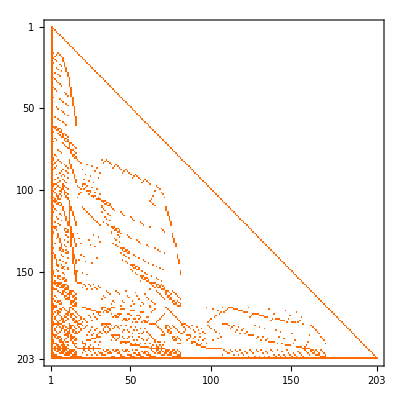

```mathematica
mat=Table[
FullBaseCoeff6[allGraphs6[k,"colofour"]],
{k,theGens}
];MatrixPlot[mat]
```

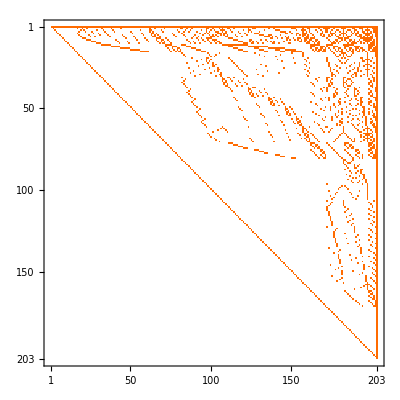

```mathematica
mat2=Table[
FullBaseCoeff6[allGraphs6[k,"colofour"]],
{k,Sort[allGraphs6NullAtomKeys,CompareSymbols[allGraphs6[#1,"colofourrealnull"],allGraphs6[#2,"colofourrealnull"]]&]}
];MatrixPlot[mat2]
```

```mathematica
mat==Transpose[mat2]
```

True